## use blackman from http://mathworld.wolfram.com/BlackmanFunction.html and corresponding instrumentation function for fit.

```mathematica
Clear["Global`*"]
us=10^-6;
tRaman=50 us;
ampF4=.115;
square=(HeavisideTheta[t]-HeavisideTheta[t-tRaman]);

blackman=ampF4 square(-1/2 Cos[2π t/tRaman]+2/25 Cos[4π t/tRaman]+21/50);
FWHM=tRaman ;
σ=.42 FWHM/(√(2π));
t0=tRaman/2;
gauss=ampF4 Exp[-(t-t0)^2/(2 σ^2)];
```

2.415×10^-6

2.415×10^-6-2.63395×10^-21 ⅈ

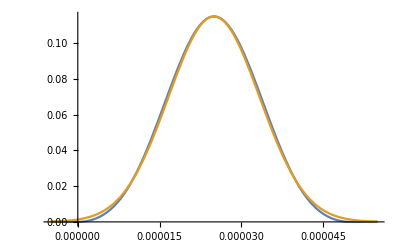

```mathematica
Integrate[blackman,{t,-Infinity,Infinity}]
Integrate[gauss,{t,-Infinity,Infinity}]
Plot[{blackman,gauss},{t,-.1 tRaman,1.1tRaman}]
```

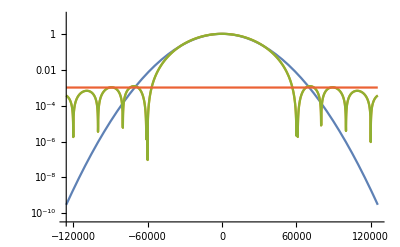

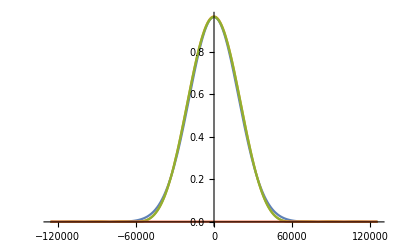

```mathematica
ftbm1=FourierTransform[blackman,t,ω]1/us/.ω->2π f;
ftg=FourierTransform[gauss,t,ω]1/us/.ω->2π f;
ftbm2=1.15((0.84-0.36 (tRaman/2)^2 f^2)Sinc[π tRaman f])/((1-(tRaman/2)^2 f^2)(1-4 (tRaman/2)^2 f^2));

LogPlot[{Abs[ftg],Abs[ftbm2],Abs[ftbm1],1 10^-3},{f,-(2π)/tRaman,(2π)/tRaman}]
Plot[{Abs[ftg],Abs[ftbm2],Abs[ftbm1],1 10^-3},{f,-(2π)/tRaman,(2π)/tRaman}]
```